# Chemical potential plots

## Brian Cowan, July 2019

## Set options to make plots look nice

```mathematica
SetOptions[{Plot,ContourPlot,LogLinearPlot, ListPlot, ListLogLinearPlot,LogLogPlot , ListLogPlot, ParametricPlot,LogPlot, PolarPlot}, BaseStyle->{FontFamily->"Euclid", FontSize->16, PointSize->0.02, FontColor->Black},AxesStyle->Directive[Black],TicksStyle->Directive[Black]];
```

## Define the chemical potential and fugacity functions

```mathematica
muF1d[tau_]:=tau InverseFunction[Function[zz,-(Sqrt[Pi]/2 PolyLog[1/2,-Exp[zz]])]][tau^(-1/2)]
```

```mathematica
zF1d[tau_]:=InverseFunction[Function[z,-(Sqrt[Pi]/2 PolyLog[1/2,-z])]][tau^(-1/2)]
```

```mathematica
muB1d[tau_]:=Re[tau InverseFunction[Function[zz,(Sqrt[Pi]/2 PolyLog[1/2,Exp[zz]])]][tau^(-1/2)]]
```

```mathematica
zB1d[tau_]:=InverseFunction[Function[z,(Sqrt[Pi]/2 PolyLog[1/2,z])]][tau^(-1/2)]
```

```mathematica
muM1d[tau_]:= tau Log[2/Sqrt[Pi tau]]
```

```mathematica
zM1d[tau_] := 2/Sqrt[Pi tau]
```

```mathematica
muF2d[tau_]:=tau Log[Exp[1/tau]-1]
```

```mathematica
muB2d[tau_]:=tau Log[1-Exp[-1/tau]]
```

```mathematica
muM2d[tau_] := -tau Log[tau]
```

```mathematica
muF3d[tau_]:=tau InverseFunction[Function[zz,-(3 Sqrt[Pi]/4 PolyLog[3/2,-Exp[zz]])]][tau^(-3/2)]
```

```mathematica
muM3d[tau_] := tau Log[4/3/Sqrt[Pi]/tau^(3/2)]
```

```mathematica
muB3d[tau_]:=If[tau>(3 Sqrt[Pi]/4 PolyLog[3/2,1])^(-2/3),tau InverseFunction[Function[zz,(3 Sqrt[Pi]/4 PolyLog[3/2,Exp[zz]])]][tau^(-3/2)],0]
```

## Plots -- exact expressions

### 1d

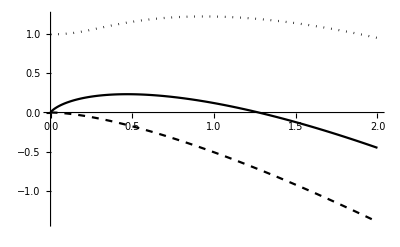

```mathematica
Plot[{muF1d[t], muB1d[t], muM1d[t]},{t,0,2},PlotStyle->{{Black, Dotted},{Black, Dashed}, Black}]
```

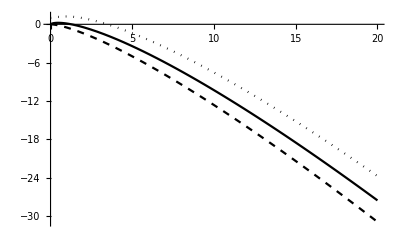

```mathematica
Plot[{muF1d[t], muB1d[t], muM1d[t]},{t,0,20},PlotStyle->{{Black, Dotted},{Black, Dashed}, Black}]
```

### 2d

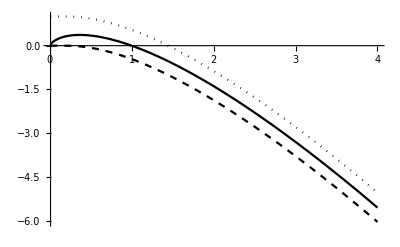

```mathematica
Plot[{muF2d[t], muB2d[t], muM2d[t]},{t,0.01,4}, PlotStyle->{{Black, Dotted},{Black, Dashed}, Black}]
```

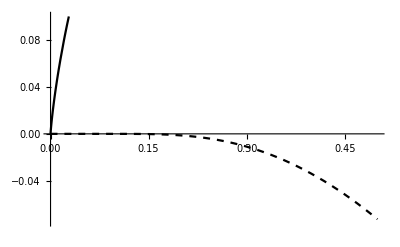

```mathematica
Plot[{muF2d[t], muB2d[t], muM2d[t]},{t,0,0.5}, PlotStyle->{{Black, Dotted},{Black, Dashed}, Black}, PlotRange->{-0.075, 0.1}]
```

#### 3d

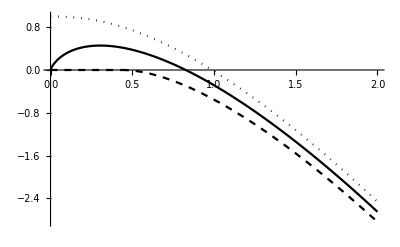

```mathematica
Plot[{muF3d[t], muB3d[t], muM3d[t]},{t,0,2}, PlotStyle->{{Black, Dotted},{Black, Dashed}, Black}]
```

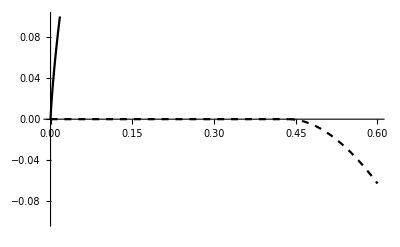

```mathematica
Plot[{muF3d[t], muB3d[t], muM3d[t]},{t,0,0.6}, PlotStyle->{{Black, Dotted},{Black, Dashed}, Black}, PlotRange->{-0.1,0.1}]
```

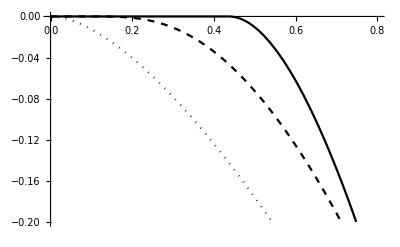

```mathematica
Plot[{muB1d[t], muB2d[t], muB3d[t]},{t,0,0.8}, PlotStyle->{{Black, Dotted},{Black, Dashed}, Black}, PlotRange->{-0.2,0}]
```

## Plots -- series expansions

### Fermions in 1d

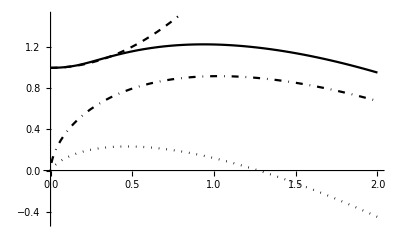

```mathematica
Plot[{muF1d[t], 1+Pi^2 t^2/12,muM1d[t],muM1d[t]+Sqrt[2 t/Pi] },{t,0,2},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-0.5, 1.5}]
```

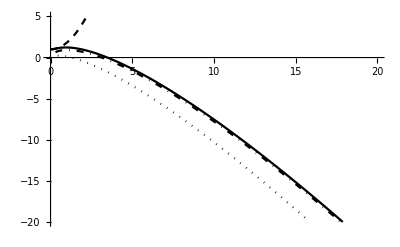

```mathematica
Plot[{muF1d[t], 1+Pi^2 t^2/12,muM1d[t],muM1d[t]+Sqrt[2 t/Pi] },{t,0,20},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-20,5}]
```

### Bosons in 1d

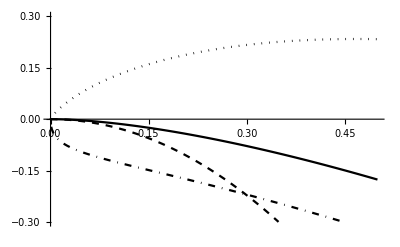

```mathematica
Plot[{muB1d[t], -Pi^2 t^2/4,muM1d[t],muM1d[t]-Sqrt[2 t/Pi] },{t,0,0.5},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-0.3, 0.3}]
```

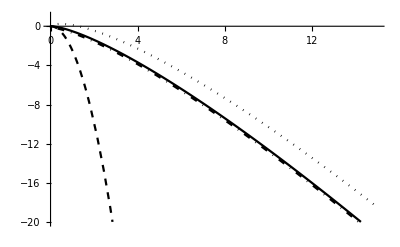

```mathematica
Plot[{muB1d[t], -Pi^2 t^2/4,muM1d[t],muM1d[t]-Sqrt[2 t/Pi] },{t,0,15},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-20, 1}]
```

### Fermions in 2d

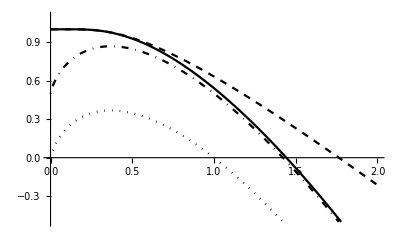

```mathematica
Plot[{muF2d[t], 1- t Exp[-1/t],muM2d[t],muM2d[t]+1/2 },{t,0,2},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-0.5, 1.1}]
```

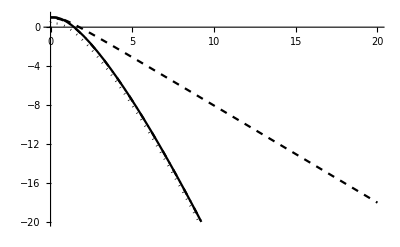

```mathematica
Plot[{muF2d[t], 1- t Exp[-1/t],muM2d[t],muM2d[t]+1/2 },{t,0,20},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-20, 1.1}]
```

### Bosons in 2d

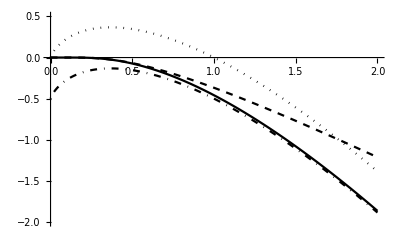

```mathematica
Plot[{muB2d[t], - t Exp[-1/t],muM2d[t],muM2d[t]-1/2 },{t,0,2},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-2, 0.5}]
```

### Fermions in 3d

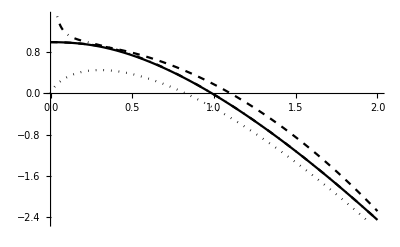

```mathematica
Plot[{muF3d[t], 1-Pi^2 t^2/12,muM3d[t],muM3d[t]+Sqrt[2/Pi/t]/3},{t,0,2},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-2.5, 1.5}]
```

### Bosons in 3d

#### First get the BEC temperature

```mathematica
tb = (3Sqrt[Pi]Zeta[3/2]/4)^(-2/3)
```

(2 (2/π)^(1/3))/(3 Zeta[3/2])^(2/3)

```mathematica
tb //N
```

0.436066

```mathematica
muB3ds[t_] := If[t<tb,0,-9Zeta[3/2]^2 (t-tb)^2/(16 Pi tb)]
```

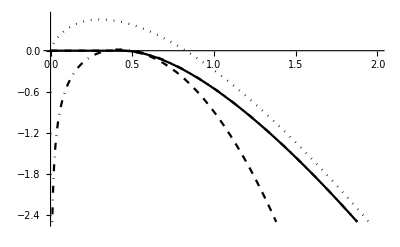

```mathematica
Plot[{muB3d[t], muB3ds[t],muM3d[t],muM3d[t]-Sqrt[2/Pi/t]/3},{t,0,2},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-2.5, 0.5}]
```

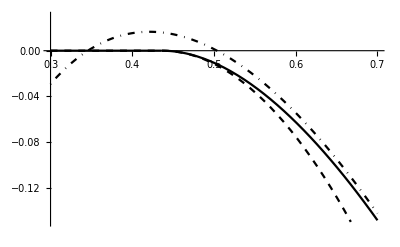

```mathematica
Plot[{muB3d[t], muB3ds[t],muM3d[t],muM3d[t]-Sqrt[2/Pi/t]/3},{t,0.3,0.7},PlotStyle->{{Black},{Black, Dashed}, {Black, Dotted},{Black, DotDashed}}, PlotRange->{-0.15,0.03}]
```